```mathematica
loadTable[path_]:= Import[NotebookDirectory[]<>path, "Table"]
```

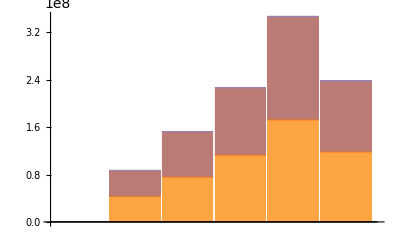

```mathematica
tabA = loadTable["/outputs/5VM_real.p1.400.out"];



BarChart[tabA, ChartLayout->"Stacked"]
```

```mathematica
Drop[tabA, 1]
```

{{2,43012185,357488,82863,0.811825,43369675,115,17,0.871212},{3,74986368,1133757,292643,0.794838,76120128,405,95,0.81},{4,111390373,1841890,254849,0.878455,113232267,697,158,0.815205},{5,171174609,2083292,280720,0.881253,173257906,743,176,0.808488},{6,117877615,1094393,120238,0.901009,118972014,413,68,0.858628}}